# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## 1. Individuals

## Generating Population

### Nodes

#### kmActivationFunc

```mathematica
kmActivationFunc[id_]:=
Switch[id,
-1,0&,
0, #&,
1,Tanh,
2,LogisticSigmoid,
3,Sin,
4,UnitStep,
5,Ramp
]
```

#### kmNode

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
ClearAll[kmNode]
kmNode[id_,layer_,func_:False,totalFuncs_:5]:=<|
"nodeId"->id,
"layer"->layer,
"inputSum"->0,
"bias"->RandomReal[{-1,1}],
"activationFunc"->If[func===False,RandomInteger[totalFuncs],func],
"output"->0
|>
```

```mathematica
ClearAll[kmNodeOutput]
kmNodeOutput[node_,prevNodes_]:=
Join[node,<|"inputSum"->#,"output"->node["bias"]+kmActivationFunc[node["activationFunc"]][#]|>]&[Total[prevNodes⟦All,"output"⟧]]
```

```mathematica
kmNode[1,1]
kmNodeOutput[%,{kmNode[2,1]~Join~<|"output"->12|>,kmNode[3,2]~Join~<|"output"->2|>}]
```

<|nodeId→1,layer→1,inputSum→0,bias→0.600685,activationFunc→0,output→0|>

<|nodeId→1,layer→1,inputSum→14,bias→0.600685,activationFunc→0,output→14.6007|>

```mathematica
kmNodeOutput[kmNode[1,1],{}]
```

<|nodeId→1,layer→1,inputSum→0,bias→-0.196276,activationFunc→0,output→-0.196276|>

### Connections

```mathematica
CantorPairing[x_,y_]:=((x+y)(x+y+1))/2+y
```

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[{in_,out_},weight_:1]:=<|
"input"->in,
"output"->out,
"weight"->RandomReal[{-weight,weight}],
"enabled"->True,
"inovation"->CantorPairing[in,out]
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

```mathematica
ClearAll[kmIndividual]
kmIndividual[input_,output_,hidden_:0]:=
<|
"input"->input,
"output"->output,
"total"->input+output,
"fitness"->∞,
"nodes"->Join[
kmNode[#,1,0]&/@Range[input],
kmNode[#,2]&/@(input+Range[output])
],
"connections"->(kmConnection[#]&/@
Flatten[
Outer[
{#1,#2}&,
Range[input],
Range[input+1,input+output]
],1])
|>
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,size_:10,options___]:=<|
"input"->in,
"output"->out,
"best"-><|"fitness"->+∞|>,
"history"->{},
"size"->size,
(*"inovations"->{},*)
"individuals"->Array[kmIndividual[in,out]&,size],
"state"->{0,0,0},
"params"-><|
"updNodeRate"->0.8,
"updConnRate"->0.2,
"addConnRate"->0.95,
"removeConnRate"->0.1,
"addNodeRate"->0.01,
"removeNodeRate"->0.15,
"crossOverRate"->0.24
|>
|>~Join~options
```

### Tests

```mathematica
testPop=kmPopulation[2,3];
```

## Individual decoding

### Connection' s logics

#### kmFindNode

```mathematica
kmFindNode[individual_,id_]:=
First@FirstPosition[individual["nodes"],<|"nodeId"->id,___|>]
```

```mathematica
kmFindNode[testPop["individuals"]⟦1⟧,3]
```

3

#### kmInNodes

Finds all nodes which are  IN nodes for the node

```mathematica
kmInNodes[nodeId_,connections_]:=
Reap[
If[nodeId==#["output"],Sow[#["input"]]]&/@connections;
]//Last//Flatten
```

```mathematica
kmInNodes[2,{kmConnection[{1,2}],kmConnection[{3,2}]}]
```

{1,3}

#### kmExistConnectionQ

```mathematica
kmExistConnectionQ[connection:{in_,out_},connections_]:= 
Or@@({#["input"],#["output"]}==connection&/@connections)
```

### Prepare for evaluation

#### kmNodesToLayers

```mathematica
ClearAll[kmNodesToLayers]
kmNodesToLayers[individual_]:=
Module[
{maxLayer=Max[individual[["nodes",All,"layer"]]],
nodes
},
Join[individual,
<|
"maxLayer"->maxLayer,
"nodesLayered"->(Function[{layer},Select[individual["nodes"],#["layer"]==layer&]]/@Range[maxLayer])
|>
]
]
```

#### kmIndividualsToLayers

```mathematica
ClearAll[kmIndividualsPrepare]
SetAttributes[kmIndividualsPrepare,HoldFirst]
kmIndividualsPrepare[population_]:=
population⟦"individuals"⟧=kmNodesToLayers[#]&/@population["individuals"]
```

```mathematica
kmIndividualsPrepare[testPop];
```

#### kmGetNodesLayered

```mathematica
ClearAll[kmGetNodesLayered]
kmGetNodesLayered[individual_,nodeIds_]:=
Flatten[Function[{nodeId},Select[individual["nodesLayered"]//Flatten,#["nodeId"]==nodeId&,1]]/@nodeIds]
```

#### kmInNodesLayered

```mathematica
ClearAll[kmInNodesLayered]
kmInNodesLayered[individual_,node_]:=kmGetNodesLayered[individual,kmInNodes[node["nodeId"],individual["connections"]]]
```

```mathematica
kmInNodesLayered[testPop["individuals"][[1]],<|"nodeId"->3,"layer"->1,"inputSum"->0,"bias"->-0.012840107337042994,"activationFunc"->0,"output"->1|>]
```

{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.765742,activationFunc→0,output→0|>}

### Evaluation

#### kmInitFirstLayer

```mathematica
ClearAll[kmInitFirstLayer]
kmInitFirstLayer[nodes_,inputs_List]:=
MapThread[Join[#1,<|"output"->#2|>]&,{SortBy[Take[nodes,Length[inputs]],#["nodeId"]&],inputs}]
```

#### kmIndividualEvaluate

```mathematica
ClearAll[kmIndividualEvaluate]
kmIndividualEvaluate[individual_,inputs_:{_,_}]:=
Module[
{individualCopy=individual},

individualCopy[["nodesLayered",1]]=kmInitFirstLayer[individualCopy["nodesLayered"]//First,inputs];
Function[{layer},
individualCopy[["nodesLayered",layer]]=
Function[{node},
kmNodeOutput[node,kmInNodesLayered[individualCopy,node]]
]/@individualCopy[["nodesLayered",layer]]
]/@Range[2,individual["maxLayer"]];
kmGetNodesLayered[individualCopy,Range[#+1,#+individual["output"]]&[individual["input"]]]⟦All,"output"⟧
]
```

```mathematica
kmIndividualEvaluate[popClassTest["individuals"][[9]],{.1,.2}]
```

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,layer_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,layer},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

Graph

### Population viewing

## Population operations

### kmAddConnection

```mathematica
SetAttributes[kmAddConnection,HoldFirst]
kmAddConnection[population_,individualId_,conn:{in_,out_}]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
existId=Position[population[["individuals",individualId,"connections"]],_?(#["input"]==in&&#["output"]==out&)]
},
If[Length[existId]==0,
individual⟦"connections"⟧=Join[
individual["connections"],
If[individual["nodes"]⟦kmFindNode[individual,in],"layer"⟧<individual["nodes"]⟦kmFindNode[individual,out],"layer"⟧,{kmConnection[conn]},{}]
];,
individual⟦"connections",existId//Last⟧=kmConnection[conn]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection, oldOutNodePos
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;

oldOutNodePos=kmFindNode[individual,connection["output"]];
individual⟦"total"⟧+=1;
individual⟦"nodes"⟧=
Append[individual["nodes"],kmNode[individual["total"],individual⟦"nodes",oldOutNodePos,"layer"⟧]];
individual⟦"nodes",oldOutNodePos,"layer"⟧+=1;

individual⟦"connections"⟧=Join[
{kmConnection[{connection["input"],#}],
kmConnection[{#,connection["output"]}]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

```mathematica
popClassTest[["individuals",4]]
```

Part::pspec1: Part specification individuals is not applicable.

popClassTest⟦individuals,4⟧

```mathematica
Position[testPop[["individuals",1,"connections"]],_?(#["input"]==1&&#["output"]==3&)]//Length
```

1

```mathematica
testPop[["individuals",1,"connections",{1}]]
```

{<|input→1,output→3,weight→-0.18526,enabled→True,inovation→13|>}

```mathematica
testPop[["individuals",1,"connections"]]
```

{<|input→1,output→3,weight→-0.18526,enabled→True,inovation→13|>,<|input→1,output→4,weight→-0.699733,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.875213,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.671778,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.622837,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.0549174,enabled→True,inovation→33|>}

### tests

```mathematica
kmAddNode[testPop,1,1]
kmAddConnection[testPop,1,{1,6}]
```

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.765742,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.299565,activationFunc→2,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.45239,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.891941,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.280634,activationFunc→1,output→0|>},connections→{<|input→1,output→6,weight→-0.909263,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.451627,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.18526,enabled→False,inovation→13|>,<|input→1,output→4,weight→-0.699733,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.875213,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.671778,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.622837,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.0549174,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.765742,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.45239,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.891941,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.280634,activationFunc→1,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.299565,activationFunc→2,output→0|>}}|>

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.765742,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.299565,activationFunc→2,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.45239,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.891941,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.280634,activationFunc→1,output→0|>},connections→{<|input→1,output→6,weight→-0.666009,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.451627,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.18526,enabled→False,inovation→13|>,<|input→1,output→4,weight→-0.699733,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.875213,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.671778,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.622837,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.0549174,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.765742,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.45239,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.891941,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.280634,activationFunc→1,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.299565,activationFunc→2,output→0|>}}|>

## Population mutations

### kmDisable Node/Conn

#### kmDisableConnection

```mathematica
ClearAll[kmDisableConnection]
kmDisableConnection[conn_]:= 
Join[conn,<|"enabled"->False|>]
```

#### kmDisableNode

```mathematica
ClearAll[kmDisableNode]
SetAttributes[kmDisableNode,HoldFirst]
kmDisableNode[population_,individualId_,nodeId_]:= 
population⟦"individuals",individualId,"connections"⟧=(Join[#2,kmDisableConnection/@#1]&@@Join[<|True->{},False->{}|>,GroupBy[population⟦"individuals",individualId,"connections"⟧,Or[#["input"]==nodeId,#["output"]==nodeId]&]])
```

### kmUpdateNode

```mathematica
ClearAll[kmUpdateNode]
SetAttributes[kmUpdateNode,HoldFirst]
kmUpdateNode[population_,individualId_,nodeId_]:= 
If[
RandomReal[]<population["params","updNodeRate"],
population["state"]=population["state"]+{0,1,0};
population[["individuals",individualId,"nodes",nodeId]]=If[
RandomReal[]<population["params","removeNodeRate"],
kmDisableNode[population,individualId,nodeId];
kmNode[#["nodeId"],#["layer"]],
kmNode[#["nodeId"],#["layer"],#["activationFunc"]]]
&[population[["individuals",individualId,"nodes",nodeId]]]
]
```

### kmMutateNodes

```mathematica
ClearAll[kmMutateNodes]
SetAttributes[kmMutateNodes,HoldFirst]
kmMutateNodes[population_,individualId_]:= 
If[
RandomReal[]<population["params","addNodeRate"],
population["state"]=population["state"]+{0,10000,0};
kmAddNode[population,individualId,RandomInteger[{1,Length[population⟦"individuals",individualId,"connections"⟧]}]],
Do[kmUpdateNode[population,individualId,RandomInteger[{1,population[["individuals",individualId,"total"]]}]],3];
population[["individuals",individualId]]=kmNodesToLayers@population[["individuals",individualId]]
]
```

```mathematica
kmMutateNodes[testPop,1]
```

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.653508,activationFunc→2,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.737262,activationFunc→2,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.45239,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.891941,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.280634,activationFunc→1,output→0|>},connections→{<|input→1,output→6,weight→-0.666009,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.451627,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.18526,enabled→False,inovation→13|>,<|input→1,output→4,weight→-0.699733,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.875213,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.671778,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.622837,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.0549174,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.490069,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.653508,activationFunc→2,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.45239,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.891941,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.280634,activationFunc→1,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.737262,activationFunc→2,output→0|>}}|>

### kmMutateConnections

```mathematica
ClearAll[kmMutateConnections]
SetAttributes[kmMutateConnections,HoldFirst]
kmMutateConnections[population_,individualId_]:= 
If[
RandomReal[]<population["params","addConnRate"],
population["state"]=population["state"]+{0,0,1};
Do[
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧],
4
];
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧]
,
population[["individuals",individualId]]
]
```

### kmCrossover

#### kmNodesFromConns

```mathematica
kmNodesFromConnections[connections_]:= 
Union[Part[connections,All,"input"],Part[connections,All,"output"]]
```

#### kmCrossover

```mathematica
ClearAll[kmCrossover]
kmCrossover[posParent1_,posParent2_]:= 
Module[
{conns1,conns2, nodes1Ids,nodes2, 
parent1,parent2,
separator= RandomChoice[
Join[posParent1["connections"],posParent2["connections"]]
]["inovation"]
},
{parent1,parent2}=RandomSample[{posParent1,posParent2}];
conns1 =Select[parent1["connections"],#["inovation"]≤separator&] ;
conns2=Select[parent2["connections"],#["inovation"]>separator&];
nodes1Ids=kmNodesFromConnections[conns1];
nodes2=Select[parent2["nodes"],!MemberQ[parent1["nodes"]⟦nodes1Ids⟧⟦All,"nodeId"⟧,#["nodeId"]]&];
(*Print[{nodes1Ids,nodes2}];*)
kmNodesToLayers@<|
"input"->parent1["input"],
"output"->parent1["output"],
"total"->Length[Join[nodes1Ids,nodes2]],
"fitness"->∞,
"nodes"->Join[parent1["nodes"]⟦nodes1Ids⟧,nodes2],
"connections"->Join[conns1,conns2]
|>
]
```

```mathematica
kmCrossover[popClassTest[["individuals",14]],popClassTest[["individuals",#]]]&/@Range[3,20];
%[[All,"nodesLayered"]]
```

```mathematica
kmCrossover[popClassTest[["individuals",14]],popClassTest[["individuals",3]]]
```

```mathematica
popClassTest[["individuals",1]]
```

## Population evolution

### Fitness

#### kmAssessFitnessAll

```mathematica
ClearAll[kmAssessFitnessAll]
SetAttributes[kmAssessFitnessAll,HoldFirst]
kmAssessFitnessAll[population_Symbol,fitness_Function]:=Module[
{min},
min=Min[population[["individuals",All,"fitness"]]=(fitness/@population["individuals"])];

If[min<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",Position[population[["individuals",All,"fitness"]],min]⟦1,1⟧⟧
]
]
]
```

#### kmAssessFitness

```mathematica
ClearAll[kmAssessFitness]
SetAttributes[kmAssessFitness,HoldFirst]
kmAssessFitness[population_Symbol,fitness_Function,individualId_]:=Module[
{fit},
fit=population[["individuals",individualId,"fitness"]]=fitness@population[["individuals",individualId]];
If[fit<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",individualId⟧
]
]
]
```

### Elimination

```mathematica
SetAttributes[kmElimination,HoldFirst]
kmElimination[population_,replaceIndividual_]:=
Block[{
index=RandomChoice[(Exp/@population[["individuals",All,"fitness"]])->Range[population["size"]]]
},
(*Print[index];*)
population⟦"individuals",index⟧=replaceIndividual;
index
]
```

### Selection

```mathematica
SetAttributes[kmSelection,HoldFirst]
kmSelection[population_]:=
RandomChoice[(#/Total[#]&)@(1/Exp/@population[["individuals",All,"fitness"]])->Range[population["size"]]]
```

### Evolution

```mathematica
ClearAll[kmEvolveOne]
SetAttributes[kmEvolveOne,HoldFirst]
kmEvolveOne[population_,fitness_]:=
Catch[
Block[{individualId=kmSelection[population]},
(*kmAssessFitness[population,fitness];*)
Which[
RandomReal[]<population⟦"params","crossOverRate"⟧,
population["state"]=population["state"]+{1,0,0};
kmAssessFitness[population,fitness,kmElimination[population,#]]&[
kmCrossover[population⟦"individuals",individualId⟧,
population⟦"individuals",RandomInteger[{1,population["size"]}]⟧
]];,
True,
kmAssessFitness[population,fitness,kmElimination[population,kmMutateNodes[population,individualId]]];
kmAssessFitness[population,fitness,kmElimination[population,kmMutateConnections[population,individualId]]];
];
individualId
]
];
```

## Test Task 1 - simple binary Classification in 2D

### kmClassificationTask – generate a task

```mathematica
ClearAll[kmClassificationTask]
kmClassificationTask[function_,testersNumber_:50,norm_:ManhattanDistance,rangeX_:{0,6},rangeY_:{-1.5,1.5}]:=
Block[{targets,
testers
},
testers =Thread[ {RandomReal[rangeX,testersNumber],RandomReal[rangeY,testersNumber]}];
targets=If[function[#1]>#2,1,0]&@@@testers;
<|"function"->function,"testers"->testers,"targets"->targets,"norm"->norm,"rangeX"->rangeX, "rangeY"->rangeY|>
]
```

```mathematica
kmClassificationTask[Sin]
```

<|function→Sin,testers→{{0.629897,0.682765},{1.63579,1.14208},{1.48002,-0.237334},{5.64836,-0.868026},{0.692824,-0.652153},{2.87321,0.338997},{3.08027,1.08618},{5.19549,-1.39511},{2.10516,-0.403091},{5.898,-0.0509225},{0.565836,-0.942887},{1.4764,1.23197},{3.19096,1.20203},{3.12689,0.878254},{2.0608,1.21983},{4.77834,0.0409383},{0.652488,-0.249712},{3.41627,-0.629228},{5.50822,0.11007},{1.27673,-0.258332},{4.00453,1.18769},{2.12551,0.433959},{2.04733,0.502515},{3.95011,1.31989},{2.07243,0.166796},{4.62656,0.913448},{1.68172,-0.474699},{3.33864,-1.1714},{1.13715,0.383584},{3.91703,0.605667},{3.01737,-1.29149},{3.09316,1.44535},{0.176829,0.573856},{1.89409,-0.972983},{1.74992,-1.43857},{5.67683,-1.13554},{4.62709,1.49533},{1.18293,1.09198},{4.26521,-0.410981},{1.52787,0.19459},{1.20225,0.624828},{0.17071,-1.22025},{2.90852,-1.13286},{1.01493,-0.662502},{3.33728,0.999907},{1.96748,0.27289},{5.79066,0.121311},{1.19479,0.277363},{4.23607,-0.800146},{0.895104,0.590402}},targets→{0,0,1,1,1,0,0,1,1,0,1,0,0,0,0,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0,1,0,0,1,1,1,0,0,0,1,1,1,1,1,0,1,0,1,0,1},norm→ManhattanDistance,rangeX→{0,6},rangeY→{-1.5,1.5}|>

### Additional functions

#### kmPredictionToAnswer

```mathematica
ClearAll[kmPredictionToAnswer]
SetAttributes[kmPredictionToAnswer,Listable]
kmPredictionToAnswer[prediction_]:=If[prediction>0.5,1,0]
```

#### kmClassificationAccuracy

```mathematica
kmClassificationAccuracy[targets_,predictions_,norm_:ManhattanDistance]:=N@norm[targets,predictions]
```

#### kmClassificationPredictions

```mathematica
kmClassificationPredictions[task_,individual_]:=LogisticSigmoid[First@kmIndividualEvaluate[individual,#]&/@task["testers"]]
```

#### kmClassificationFitness

```mathematica
kmClassificationFitness[task_]:=With[
{targets=task["targets"],testers=task["testers"]},
Function[{individual},
kmClassificationAccuracy[targets,LogisticSigmoid@kmIndividualEvaluate[individual,#]&/@testers,task["norm"]]
+Length[Flatten[individual[["nodesLayered"]]]]/100
]
]
```

### kmShowPredictions

#### NonZeroQ

```mathematica
ClearAll[NonZeroQ]
NonZeroQ[n_]:=(n=!=0)&&NumberQ[n]
```

#### kmShowTestersEpilog

```mathematica
ClearAll[kmShowTestersEpilog]
kmShowTestersEpilog[testers_,targets_,predictions_]:=
{AbsolutePointSize[11],{
Red,Point@Extract[testers,Position[targets-#,_?NonZeroQ]],
White,Point@Extract[testers,Position[targets-#,0]]},
AbsolutePointSize[7],{
Darker@Yellow,Point@Extract[testers,Position[#,0]],
Blue,Point@Extract[testers,Position[#,1]]
}
}&[kmPredictionToAnswer[predictions]]
```

#### kmShowPredictions

```mathematica
ClearAll[kmShowPredictions]
kmShowPredictions[task_,predictions_]:=
With[{
function =task["function"]
},
Labeled[
Plot[function[x],{x,Sequence@@task["rangeX"]},
Epilog->kmShowTestersEpilog[task["testers"],task["targets"],predictions],
PlotRange->{task["rangeX"],task["rangeY"]},AspectRatio->1,Axes->True,
Background->LightGray
],
"Error: "<>ToString@kmClassificationAccuracy[task["targets"],predictions,task["norm"]]
]

]
```

```mathematica
(*kmShowPredictions[classTest,RandomReal[{0,1},70]]*)
```

### Test

#### init

```mathematica
classTest=kmClassificationTask[Sin,150,EuclideanDistance,{-1,5},{-2,2}];
fitnessClassTest=kmClassificationFitness[classTest];

quant=50;
popClassTest=kmPopulation[2,1,quant];
Do[kmAddNode[popClassTest,RandomInteger[{1,quant}],RandomInteger[{1,2}]],Floor[quant*0.7]]
kmIndividualsPrepare[popClassTest];
kmAssessFitnessAll[popClassTest,fitnessClassTest];
```

{7.18979,7.0848,7.31717,7.59354,7.21055,8.71393,6.52618,7.85814,6.78064,6.80955,7.46202,6.95622,7.86221,8.65014,8.7391,8.77791,7.20653,8.81093,5.79176,8.39363,8.9059,8.7407,6.52215,6.10909,8.88499,5.32211,6.88154,7.02399,9.56992,8.59104,7.51366,7.58956,8.54067,7.09684,7.24591,5.78415,6.01166,7.53399,8.70922,7.69903,8.64267,7.60015,6.02098,8.59488,7.82697,9.53592,8.78024,8.87931,7.91583,8.82422}

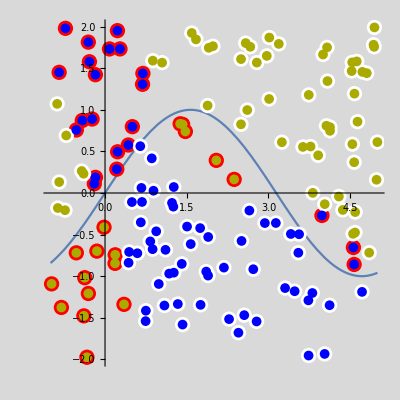
-Graphics-Error: 5.28211

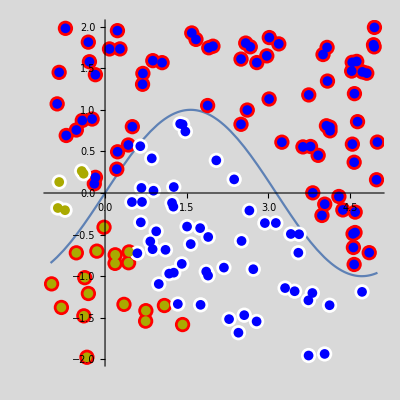
-Graphics-Error: 7.28717

{3,4,3,4,3,4,3,3,4,6,3,3,3,4,3,6,4,4,4,4,5,3,3,4,3,4,3,4,4,3,3,3,5,3,6,5,4,3,3,4,3,4,3,3,4,4,3,3,5,3}

```mathematica
popClassTest[["individuals",All,"fitness"]]
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["individuals",3]]]]
popClassTest[["individuals",All,"total"]]
```

#### Evolving

```mathematica
Monitor[
Do[kmEvolveOne[popClassTest,fitnessClassTest],{i,1000}];
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
,
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
]
```

-Graphics-Error: 5.28211

```mathematica
Dynamic[popClassTest[["state"]]]
Dynamic[popClassTest[["individuals",All,"total"]]]
Dynamic[popClassTest[["history"]]//Length]
Dynamic[popClassTest[["best"]]]
```

```mathematica
popClassTest[["best","nodesLayered"]]//Flatten//Length
```

5